```mathematica
$Assumptions={σ>0,r>0,n>0,α>2,τ>0,c>2,ψ<∞,σ<∞,μ>0,μ<∞,m>0}
```

{σ>0,r>0,n>0,α>2,τ>0,c>2,ψ<∞,σ<∞,μ>0,μ<∞,m>0}

```mathematica
(10/Log[10])/(Sqrt[2π] σ ψ)ⅇ^(-(10 Log10[ψ])^2/(2σ^2))/((10/Log[10])/(Sqrt[2π] σ ψ)ⅇ^(-(10 Log[ψ])^2/(2σ^2)))//FullSimplify
```

ⅇ^((50 (-1+Log[10]^2) Log[ψ]^2)/(σ^2 Log[10]^2))

```mathematica
pdfψ[ψ_,σ_,μ_]:=(10/Log[10])/(Sqrt[2π] σ ψ)ⅇ^(-(10 Log10[ψ]-μ)^2/(2σ^2))
```

```mathematica
Integrate[ψ^(2/α) pdfψ[ψ,σ,0],{ψ,0,∞}]
```

ⅇ^((σ^2 Log[10]^2)/(50 α^2))

```mathematica
Expectedψ2α[α_,σ_]:=(ⅇ^((σ^2 Log[10]^2)/(50 α^2)))/(√(1/σ^2) σ)
```

```mathematica
Integrate[pdfψ[ψ,σ,0],{ψ,0,ψ}]
```

1/2 (1+Erf[(5 √2 Log[ψ])/(σ Log[10])])

```mathematica
Integrate[pdfψ[ψ,σ,μ],{ψ,0,ψ}]
```

1/2 Erfc[(μ Log[10]-10 Log[ψ])/(√2 σ Log[10])]

```mathematica
cdfψ[ψ_,σ_,μ_]:=1/2 (1+Erf[(5 √2 Log[ψ])/(σ Log[10])])
```

```mathematica
cdfψ[ψ,σ,0]
```

```mathematica
1/2 (1+Erf[(5 √2 Log[ψ])/(σ Log[10])])//FullSimplify
```

1/2 (1+Erf[(5 √2 Log[ψ])/(σ Log[10])])

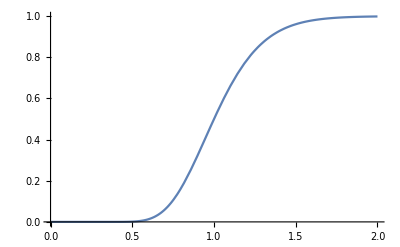

```mathematica
Plot[cdfψ[ψ,1,0],{ψ,0,2}]
```

```mathematica
Integrate[pdfψ[ψ,σ,0],{ψ,(r^α τ)/n^(α/2),∞}]
```

1/2 Erfc[(5 √2 (-1/2 α Log[n]+α Log[r]+Log[τ]))/(σ Log[10])]

```mathematica
Integrate[(π λ)/c ψ^(2/α) τ^(-2/α) pdfψ[ψ,σ,0],{ψ,((τ^(2/α) c)/(π λ))^(2α),∞}]
```

(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (1+(Erf[(√((σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4])^2))/(5 √2 α σ Log[10])] (σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4]))/(√((σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4])^2))))/(2 c)

```mathematica
Integrate[ pdfψ[ψ,σ,0],{ψ,0,((τ^(2/α) c)/(π λ))^(2α)}]
```

1/2 (1+(Erf[(5 √2 √(Log[π^(-2 α) (c/λ)^(2 α) τ^4]^2))/(σ Log[10])] √(Log[π^(-2 α) (c/λ)^(2 α) τ^4]^2))/Log[π^(-2 α) (c/λ)^(2 α) τ^4])

```mathematica
1/2 (1+(Erf[(5 √2 √(Log[π^(-2 α) (c/λ)^(2 α) τ^4]^2))/(σ Log[10])] √(Log[π^(-2 α) (c/λ)^(2 α) τ^4]^2))/Log[π^(-2 α) (c/λ)^(2 α) τ^4])+(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (1+(Erf[(√((σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4])^2))/(5 √2 α σ Log[10])] (σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4]))/(√((σ^2 Log[10]^2-50 α Log[π^(-2 α) (c/λ)^(2 α) τ^4])^2))))/(2 c)//FullSimplify
```

1/2 (1+Erf[(5 √2 Log[π^(-2 α) (c/λ)^(2 α) τ^4])/(σ Log[10])]+(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (1+Erf[(σ Log[10])/(5 √2 α)-(5 √2 Log[π^(-2 α) (c/λ)^(2 α) τ^4])/(σ Log[10])]))/c)

#### 7/26

```mathematica
Integrate[(λ π)/c τ^(-2/α)ψ^(2/α)pdfψ[ψ,σ,0],{ψ,0,∞}]//FullSimplify
```

(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α))/c

```mathematica
Integrate[(-λ π)/c τ^(-2/α)ψ^(2/α)pdfψ[ψ,σ,0] ,{ψ,τ(c/(λ π))^(α/2),∞}]//FullSimplify
```

(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (-2+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/(2 c)

```mathematica
Integrate[pdfψ[ψ,σ,0] ,{ψ,τ(c/(λ π))^(α/2),∞}]	//FullSimplify
```

1/2 Erfc[(5 √2 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ]))/(σ Log[10])]

```mathematica
1-(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α))/c+(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (-2+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/(2 c)-1/2 Erfc[(5 √2 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ]))/(σ Log[10])]//FullSimplify
```

1/2 (1+Erf[(5 √2 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ]))/(σ Log[10])]+(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (-4+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/c)

```mathematica
D[(1/2 (1+Erf[(5 √2 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ]))/(σ Log[10])]+(ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-2/α) (-4+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/c)), τ]
```

1/2 (-(2 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-1-2/α) (-4+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/(c α)+(10 ⅇ^(-(50 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ])^2)/(σ^2 Log[10]^2)) √(2/π))/(σ τ Log[10])+(10 ⅇ^((σ^2 Log[10]^2)/(50 α^2)-((σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10]))^2) √(2 π) λ τ^(-1-2/α))/(c σ Log[10]))

```mathematica
Limit[(1/2 (-(2 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-1-2/α) (-4+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/(c α)+(10 ⅇ^(-(50 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ])^2)/(σ^2 Log[10]^2)) √(2/π))/(σ τ Log[10])+(10 ⅇ^((σ^2 Log[10]^2)/(50 α^2)-((σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10]))^2) √(2 π) λ τ^(-1-2/α))/(c σ Log[10]))),c->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
Limit[(1/2 (-(2 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-1-2/α) (-4+Erfc[(σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10])]))/(c α)+(10 ⅇ^(-(50 (-1/2 α Log[π]+Log[(c/λ)^(α/2)]+Log[τ])^2)/(σ^2 Log[10]^2)) √(2/π))/(σ τ Log[10])+(10 ⅇ^((σ^2 Log[10]^2)/(50 α^2)-((σ Log[10])/(5 √2 α)+(5 (α Log[π]-2 Log[(c/λ)^(α/2) τ]))/(√2 σ Log[10]))^2) √(2 π) λ τ^(-1-2/α))/(c σ Log[10])))c,c->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(2 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-(2+α)/α))/α

#### 7/30

```mathematica
Integrate[τ/(1+m τ)1/2 (-(2 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) π λ τ^(-1-2/α) (-4))/(c α)),{τ,0,∞}]
```

(4 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) m^(-1+2/α) π^2 λ Csc[(2 π)/α])/(c α)

```mathematica
Solve[m(4 ⅇ^((σ^2 Log[10]^2)/(50 α^2)) m^(-1+2/α) π^2 λ Csc[(2 π)/α])/α==1 ,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→(2 π)^-α ((ⅇ^(-(σ^2 Log[10]^2)/(50 α^2)) α Sin[(2 π)/α])/λ)^(α/2)}}